```mathematica
SetOptions[{ Plot, LogPlot, LogLinearPlot, LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 20},ImageSize-> 600,PlotStyle-> {{Thick,Darker@Red},{Thick,Darker@Blue},{Thick,Darker@Green}, {Thick, Darker@Magenta}, {Thick,Darker@Cyan}},
Axes-> False,Frame-> True];
```

```mathematica
v[θ_, ϕ_]:=Sqrt[2] Cos[θ+ϕ]
```

```mathematica
p[θ_]= v[θ,0]*v[θ,0]/10+v[θ,-120Degree]*v[θ,-120Degree]/10+v[θ,120Degree]*v[θ,120Degree]/10
```

Cos[θ]^2/5+1/5 Sin[30 °-θ]^2+1/5 Sin[30 °+θ]^2

```mathematica
FullSimplify[p[θ]]
```

3/10

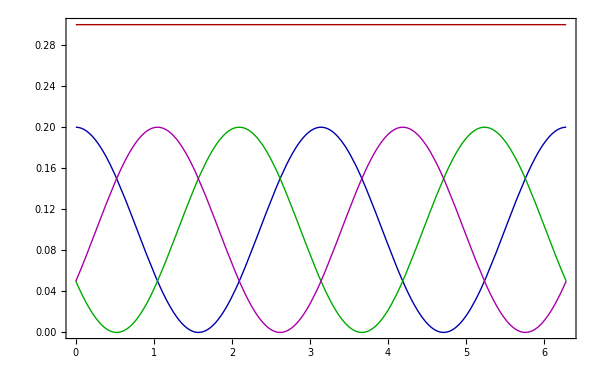

```mathematica
Plot[{p[θ],v[θ,0]*v[θ,0]/10,v[θ,-120Degree]*v[θ,-120Degree]/10,v[θ,120Degree]*v[θ,120Degree]/10},  {θ,0, 2π}]
```